# RSJ model with serial resistance

Effective RSJ model under a biharmonic voltage drive, with a series resistor. The phase obeys a first-order equation; the calculated mean phase velocity and current give the voltage-current trace. See Sec. 7 (Effective RSJ model) of https://arxiv.org/pdf/2610.05536 for the physical model and normalization.

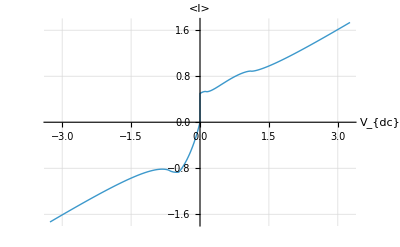

```mathematica
(* Biharmonic drive: fundamental Vac, second harmonic Vac2, relative phase delta; R and Rs set the resistive channels. *)
set={ω->0.001,Vac->0.666,Vac2->0.333,δ->π/2,R->2,Rs->1,periods->4,calculatePart->0.5};
(* Sweep the applied dc bias; solve the overdamped phase equation for each Vdc in parallel. *)
lineTraceC0=
ParallelTable[sol=NDSolve[{y'[x](1/R+1/Rs)==-1Cos[y[x]]+(Vdc+Vac Sin[ω x]+Vac2 Sin[2ω x+δ])/Rs,y[0]==0}/.set,y,{x,periods (2π)/ω}/.set];
{(((y[(2π)/ω periods]-y[(1-calculatePart)(2π)/ω periods])/(calculatePart(2π)/ω periods))/.sol/.set)[[1]],((Vdc-(y[(2π)/ω periods]-y[(1-calculatePart)(2π)/ω periods])/(calculatePart(2π)/ω periods))/Rs/.sol/.set)[[1]]},{Vdc,-5,5,0.005}];
(* Plot the pairs {mean phase velocity, mean current}; the phase velocity is proportional to the junction voltage. *)
ListLinePlot[lineTraceC0,PlotStyle->Thick,AxesLabel->{"V_{dc}","<I>"},PlotRange->All,GridLines->Automatic]
```

Export: lineTrace_V_I.dat is a two-column table containing the calculated mean phase velocity (junction-voltage coordinate) and the corresponding mean current. The file is written to NotebookDirectory[].

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"lineTrace_V_I.dat"}],lineTraceC0,"Table"]
```

/Users/rubenseoane/Dropbox/Talento/2026/dualDiode_Elia/lineTrace_V_I.dat

### Plotting dynamics for some cases

<y'> = 0.721003

I = 0.778997

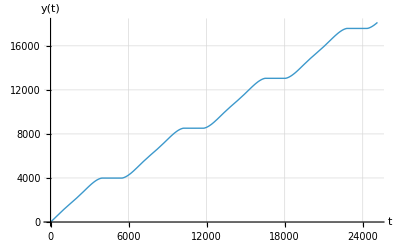

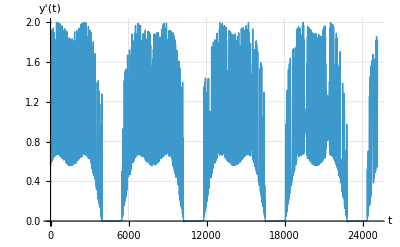

```mathematica
(* Inspect one representative dc bias Vdc0 using the same drive and resistance parameters. *)
set={ω->0.001,Vac->0.666,Vac2->0.333,δ->π/2,R->2,Rs->1,periods->4,calculatePart->0.5};
Vdc0=1.5;
tmax=periods (2 π)/ω/. set;
ysol=NDSolveValue[{y'[t] (1/R+1/Rs)==-Cos[y[t]]+(Vdc0+Vac Sin[ω t]+Vac2 Sin[2 ω t+δ])/Rs,y[0]==0}/. set,y,{t,0,tmax}];
(* Average y'(t) over the final calculatePart fraction of the trajectory to reduce transients. *)
avgYprime=(ysol[(2 π)/ω periods]-ysol[(1-calculatePart) (2 π)/ω periods])/(calculatePart (2 π)/ω periods)/. set;
current=(Vdc0-avgYprime)/(Rs/. set);
Print["<y'> = ",avgYprime];
Print["I = ",current];
(* Plot the phase y(t) and its time derivative; the mean current is (Vdc0 - <y'>)/Rs. *)
Plot[ysol[t],{t,0,tmax},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","y(t)"},GridLines->Automatic]
Plot[ysol'[t],{t,0,tmax},PlotRange->All,PlotStyle->Thick,AxesLabel->{"t","y'(t)"},GridLines->Automatic]
```